```mathematica
PlotComplexRoots[z_?NumberQ,n_?IntegerQ,imSize_?IntegerQ]:=
Module[
{r=Abs[z],θ=Arg[z],roots,g1,g2,g3,nRootR},
nRootR=r^(1/n);
roots=Table[
nRootR Exp[I(θ/n+(2π k)/n)],
{k,0,n-1}];
g1=ComplexListPlot[Callout[#,#]&/@roots,PlotRange->nRootR+0.5,PlotStyle->96,ImageSize->imSize];
g2=Graphics[#,ImageSize->imSize]&@Circle[{0,0},nRootR];
g3=Graphics[{Arrowheads[0.02],#}]&/@Arrow/@Thread[{Table[{0,0},n],Thread[{Re/@roots,Im/@roots}]}];
Show[g1,g2,g3]
]
```

```mathematica
n=4;
imSize=480;
Export[FileNameJoin[{NotebookDirectory[],"Complex_roots_1_n"<>ToString@n<>".eps"}],PlotComplexRoots[1,n,imSize]];
```

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_1/Complex_roots_1_n4.eps

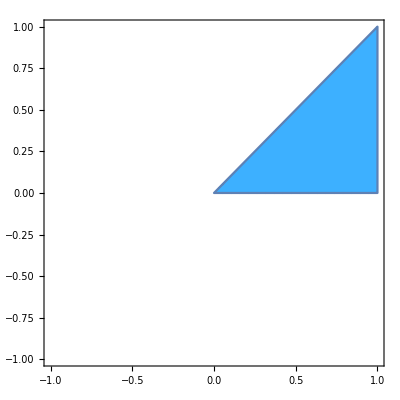

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_1/region_plot_3.eps

```mathematica
g=ComplexRegionPlot[0≤Arg[z]≤π/4,{z,-1-I,1+I},PlotStyle->96,PlotRange->1]
Export[FileNameJoin[{NotebookDirectory[],"region_plot_3"<>".eps"}],g]
```

```mathematica
cc={-0.5,-0.8}
g1=ComplexListPlot[MapThread[Callout,{{cc[[1]]+cc[[2]]I,-1-0.2I},{"z_0","z"}}],AspectRatio->1,PlotStyle->96,PlotRange->3,ImageSize->480,AxesLabel->{x,y},Ticks->None];
g2=Graphics[{{Line[{cc,{cc[[1]]+Cos[60Degree],cc[[2]]+Sin[60Degree]}}],Text["δ",{-0.45,-0.3}]},{Dashed,Circle[cc,1]}}];
Show[g1,g2]
Export[FileNameJoin[{NotebookDirectory[],"limits_def_2"<>".eps"}],Show[g1,g2]]
```

{-0.5,-0.8}

-Graphics-

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_1/limits_def_2.eps

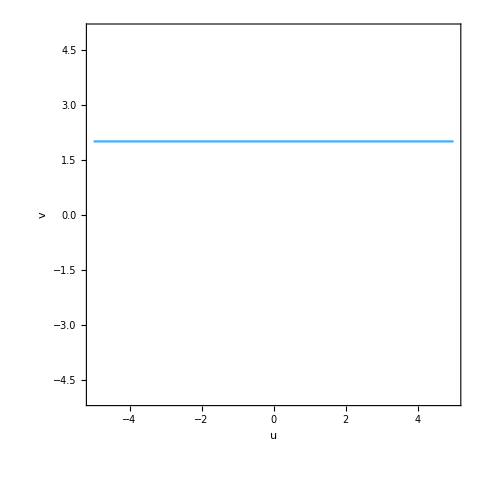

/Users/anirudh/Documents/LaTeX(2)/notes/complex_analysis/figs/chapter_1/f_map_2_4.eps

```mathematica
g2=ContourPlot[y==2,{x,-5,5},{y,-5,5},AspectRatio->1,FrameLabel->{u,v},ContourStyle->96,ImageSize->480]
Export[FileNameJoin[{NotebookDirectory[],"f_map_2_4"<>".eps"}],g2]
```

```mathematica
(*Stereographic Projection*)
```

```mathematica
gSphere= Graphics3D[{Opacity[0.4],Sphere[{0,0,0}]}];
gPoints=Graphics3D[{Point[{-2,0,0}],{Lighter@Blue,PointSize[0.02],Point[{0,1,0}]},{PointSize[0.02],Red,Point[{-2+6/5,3/5,0}]}}];
gLines=Graphics3D[Line[{{-2,0,0},{0,1,0}}]];
gLabels=Graphics3D[{Text["z",{-2,0.1,0}],Text["P",{-2+6/5,3/5+0.1,0}],Text["N",{0,1.1,0}]}];
Show[{gSphere,gPoints,gLines,gLabels},Boxed->False]
```

-Graphics3D-

```mathematica
pts=Solve[(-2-2λ)^2+λ^2==1,λ]
```

{{λ→-1},{λ→-3/5}}

```mathematica
λ[a_,b_ ,x_]:=Min[1,Max[0,(x-a)/(b-a)]]
s[a_,b_,x_]:=
Module[
{l=λ[a,b,x]},
l^2(3-2l)]
uv[i_,j_]:=50FractionalPart[{i,j}/π]
a[i_,j_]:=
Module[
{u=uv[i,j][[1]],v=uv[i,j][[2]]},
2FractionalPart[u v(u + v)]-1]
b[i_,j_]:=a[i+1,j]
c[i_,j_]:=a[i,j+1]
d[i_,j_]:=a[i+1,j+1]
n[i_,j_,x_,z_]:=a[i,j]+(b[i,j]-a[i,j])s[0,1,x-i]+(c[i,j]-a[i,j])s[0,1,z-j]+(a[i,j]-b[i,j]-c[i,j]+d[i,j])s[0,1,x-i]s[0,1,z-j]
surface[i_,j_,x_,z_]:=
Module[
{m={{4/5,-3/5},{3/5,4/5}}},
ParallelSum[1/2^k n[i,j,#1,#2]&@@(2^k MatrixPower[m,k].{x,z}),{k,5}]
]
```

```mathematica
Plot3D[surface[1,2,x,z],{x,-10,10},{z,-10,10}]
```

$Aborted

```mathematica
Show[
ParallelTable[
Plot3D[1/8 n[i,j,x,z],{x,i-1,i+1},{z,j-1,j+1},PlotRange->{{-10,10},{-10,10}}],
{i,1,10},{j,1,10}]
]
```

-Graphics3D-

```mathematica
m={{4/5,-3/5},{3/5,4/5}};
n[1,2,#1,#2]&@@(m.{1,2})
```

-1+13/125 (-2 (-24188+750000/π^3)+2 (-48377+1500000/π^3))+2 (-24188+750000/π^3)

```mathematica
f[3,#1,#2]&@@{1,2}
```

f[3,1,2]